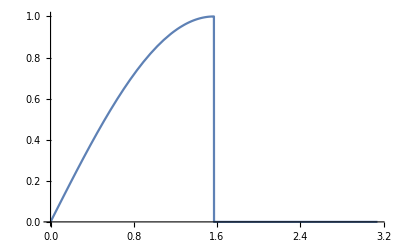

```mathematica
Plot[Sin[t](1 -UnitStep[t-Pi/2]),{t, 0, Pi}]
```

```mathematica
paso1=LaplaceTransform[x''[t]+x[t] == Sin[t](1-UnitStep[t-Pi/2]), t, s]
```

LaplaceTransform[x[t],t,s]+s^2 LaplaceTransform[x[t],t,s]-s x[0]-x'[0]==1/(1+s^2)-(ⅇ^(-(π s)/2) s)/(1+s^2)

```mathematica
paso2 = paso1 /.{x[0]->0, x'[0]->0}
```

LaplaceTransform[x[t],t,s]+s^2 LaplaceTransform[x[t],t,s]==1/(1+s^2)-(ⅇ^(-(π s)/2) s)/(1+s^2)

```mathematica
paso3 = Solve[paso2, LaplaceTransform[x[t],t, s]]
```

{{LaplaceTransform[x[t],t,s]→(ⅇ^(-(π s)/2) (ⅇ^((π s)/2)-s))/((1+s^2)^2)}}

```mathematica
sol=InverseLaplaceTransform[paso3,s, t]
```

{{x[t]→1/2 (-t Cos[t]+(-π/2+t) Cos[t] HeavisideTheta[-π/2+t]+Sin[t])}}

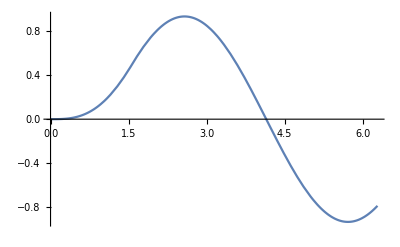

```mathematica
Plot[x[t]/.sol,{t, 0, 2 Pi}]
```